# QCD calculation: Webber et al. Sec. 7

-Graphics-

## Two-jet cross sections (Only QCD; mass ignored) : Ellis-Stirling-Webber Sec.7.5

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
SetDirectory[FileNameJoin[{$HomeDirectory,"Documents","Dropbox","FeynLecture"}]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.7

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 4 Jan 12

FormCalc 7.3

by Thomas Hahn

last revised 12 Jan 12

### Create Topology (and also ignore helicities)

```mathematica
topologies=CreateTopologies[0,2->2];
_Hel=0;
```

### q q' -> q q'

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/Lorentz.gen

> $SVMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/SMQCD.mod

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/SM.mod

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 120 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

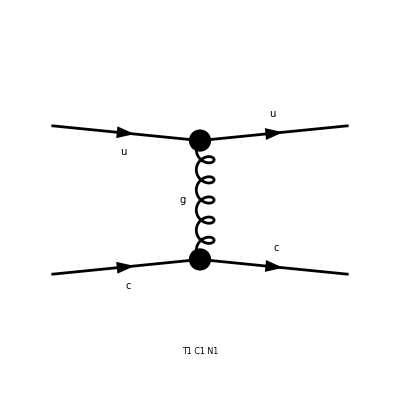

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
```

```mathematica
SquaredME[amp]//.HelicityME[amp]//FullSimplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

2/9 Alfas2 π^2 (2 (MC2+MU2-S)^2+2 S T+T^2) Den[T,0]^2 (Mat[SUN1,SUN1]-3 (Mat[SUN1,SUN2]+Mat[SUN2,SUN1]-3 Mat[SUN2,SUN2]))

```mathematica
%//.Abbr[]
```

2/9 Alfas2 π^2 (2 (MC2+MU2-S)^2+2 S T+T^2) Den[T,0]^2 (-3 (-3 Mat[SUNT[Col1,Col4] SUNT[Col2,Col3],SUNT[Col1,Col4] SUNT[Col2,Col3]]+Mat[SUNT[Col1,Col4] SUNT[Col2,Col3],SUNT[Col1,Col3] SUNT[Col2,Col4]]+Mat[SUNT[Col1,Col3] SUNT[Col2,Col4],SUNT[Col1,Col4] SUNT[Col2,Col3]])+Mat[SUNT[Col1,Col3] SUNT[Col2,Col4],SUNT[Col1,Col3] SUNT[Col2,Col4]])

```mathematica
SquaredME[amp]//.HelicityME[amp]//.ColourME[amp]//FullSimplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

16 Alfas2 π^2 (2 (MC2+MU2-S)^2+2 S T+T^2) Den[T,0]^2

```mathematica
%//.{Alfas2->(gs^2/(4π))^2,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}
```

(gs^4 (2 S^2+2 S T+T^2))/T^2

```mathematica
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

ggggg..................
HelicityME takes AVARAGE, and ColourME takes SUM!!!!!!!!!!!!!!

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

```mathematica
FullSimplify[(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2^2/3^2//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### q q' -> q q' (Again)

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
FullSimplify[(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2^2/3^2//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

-Graphics-

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM... running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

ok

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### g q -> g q

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

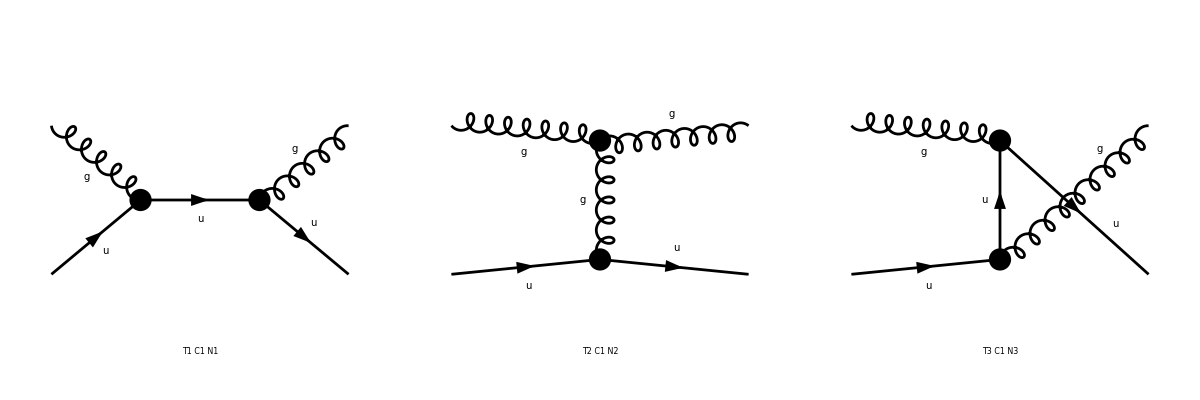

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM... running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

ok

1/12 (256/3 Alfas2 π^2 (-2 AbbSum10-AbbSum8 MU2+AbbSum7 S+(AbbSum9 T)/2-1/2 AbbSum6 (MU2-S) (MU2-U)-(Abb13 U)/2) Den[S,MU2]^2+64/3 Alfas π (1/2 Abb37 (-MU2+S)+(Abb36 T)/2) Den[S,MU2] (4 Alfas Pair1 π Den[S,MU2]+8 Alfas Pair1 π Den[T,0])+64/3 Alfas π (1/2 AbbSum15 (-MU2+S)+(AbbSum14 T)/2) Den[S,MU2] (-4 Alfas Pair2 π Den[S,MU2]-8 Alfas Pair2 π Den[T,0])+64/3 Alfas π (-AbbSum20+1/2 AbbSum19 (-MU2+S)-(AbbSum21 T)/2) Den[S,MU2] (-8 Alfas Pair3 π Den[S,MU2]-8 Alfas Pair4 π Den[T,0])+64/3 Alfas π (1/2 Abb8 (-MU2+S)+(Abb7 T)/2) Den[S,MU2] (4 Alfas π (Pair1Superscript[*]) Den[S,MU2]+8 Alfas π (Pair1Superscript[*]) Den[T,0])-8/3 (MU2-S) (MU2-U) (4 Alfas Pair1 π Den[S,MU2]+8 Alfas Pair1 π Den[T,0]) (4 Alfas π (Pair1Superscript[*]) Den[S,MU2]+8 Alfas π (Pair1Superscript[*]) Den[T,0])+16/3 (AbbSum13 (-MU2+S)+(Pair3 T)/2) (-4 Alfas Pair2 π Den[S,MU2]-8 Alfas Pair2 π Den[T,0]) (4 Alfas π (Pair1Superscript[*]) Den[S,MU2]+8 Alfas π (Pair1Superscript[*]) Den[T,0])+16/3 ((AbbSum18 MU2)/2+1/2 Pair7 (2 S+T)-(Pair2 U)/2) (-8 Alfas Pair3 π Den[S,MU2]-8 Alfas Pair4 π Den[T,0]) (4 Alfas π (Pair1Superscript[*]) Den[S,MU2]+8 Alfas π (Pair1Superscript[*]) Den[T,0])+64/3 Alfas π (1/2 AbbSum2 (-MU2+S)+(AbbSum1 T)/2) Den[S,MU2] (-4 Alfas π (Pair2Superscript[*]) Den[S,MU2]-8 Alfas π (Pair2Superscript[*]) Den[T,0])+16/3 (AbbSum22 (-MU2+S)+(Pair10 T)/2) (4 Alfas Pair1 π Den[S,MU2]+8 Alfas Pair1 π Den[T,0]) (-4 Alfas π (Pair2Superscript[*]) Den[S,MU2]-8 Alfas π (Pair2Superscript[*]) Den[T,0])+16/3 (2 AbbSum11-T/2) (-4 Alfas Pair2 π Den[S,MU2]-8 Alfas Pair2 π Den[T,0]) (-4 Alfas π (Pair2Superscript[*]) Den[S,MU2]-8 Alfas π (Pair2Superscript[*]) Den[T,0])+16/3 (AbbSum16+(Pair6 T)/2) (-8 Alfas Pair3 π Den[S,MU2]-8 Alfas Pair4 π Den[T,0]) (-4 Alfas π (Pair2Superscript[*]) Den[S,MU2]-8 Alfas π (Pair2Superscript[*]) Den[T,0])+64/3 Alfas π (-AbbSum5+1/2 AbbSum3 (-MU2+S)-(AbbSum4 T)/2) Den[S,MU2] (-8 Alfas π (Pair3Superscript[*]) Den[S,MU2]-8 Alfas π (Pair4Superscript[*]) Den[T,0])+16/3 ((AbbSum23 MU2)/2+1/2 Pair12 (2 S+T)-(Pair9 U)/2) (4 Alfas Pair1 π Den[S,MU2]+8 Alfas Pair1 π Den[T,0]) (-8 Alfas π (Pair3Superscript[*]) Den[S,MU2]-8 Alfas π (Pair4Superscript[*]) Den[T,0])+16/3 (AbbSum12+(Pair8 T)/2) (-4 Alfas Pair2 π Den[S,MU2]-8 Alfas Pair2 π Den[T,0]) (-8 Alfas π (Pair3Superscript[*]) Den[S,MU2]-8 Alfas π (Pair4Superscript[*]) Den[T,0])+16/3 (AbbSum17-T/2) (-8 Alfas Pair3 π Den[S,MU2]-8 Alfas Pair4 π Den[T,0]) (-8 Alfas π (Pair3Superscript[*]) Den[S,MU2]-8 Alfas π (Pair4Superscript[*]) Den[T,0])-64/3 Alfas2 π^2 (-2 AbbSum10-AbbSum8 MU2+AbbSum7 S+(AbbSum9 T)/2-1/2 AbbSum6 (MU2-S) (MU2-U)-(Abb13 U)/2) Den[S,MU2] Den[U,MU2]-8/3 Alfas π (1/2 Abb37 (-MU2+S)+(Abb36 T)/2) (4 Alfas Pair1 π Den[S,MU2]+8 Alfas Pair1 π Den[T,0]) Den[U,MU2]-8/3 Alfas π (1/2 AbbSum15 (-MU2+S)+(AbbSum14 T)/2) (-4 Alfas Pair2 π Den[S,MU2]-8 Alfas Pair2 π Den[T,0]) Den[U,MU2]-8/3 Alfas π (-AbbSum20+1/2 AbbSum19 (-MU2+S)-(AbbSum21 T)/2) (-8 Alfas Pair3 π Den[S,MU2]-8 Alfas Pair4 π Den[T,0]) Den[U,MU2]-8/3 Alfas π (1/2 Abb8 (-MU2+S)+(Abb7 T)/2) (4 Alfas π (Pair1Superscript[*]) Den[S,MU2]+8 Alfas π (Pair1Superscript[*]) Den[T,0]) Den[U,MU2]-8/3 Alfas π (1/2 AbbSum2 (-MU2+S)+(AbbSum1 T)/2) (-4 Alfas π (Pair2Superscript[*]) Den[S,MU2]-8 Alfas π (Pair2Superscript[*]) Den[T,0]) Den[U,MU2]-8/3 Alfas π (-AbbSum5+1/2 AbbSum3 (-MU2+S)-(AbbSum4 T)/2) (-8 Alfas π (Pair3Superscript[*]) Den[S,MU2]-8 Alfas π (Pair4Superscript[*]) Den[T,0]) Den[U,MU2]+256/3 Alfas2 π^2 (-2 AbbSum10-AbbSum8 MU2+AbbSum7 S+(AbbSum9 T)/2-1/2 AbbSum6 (MU2-S) (MU2-U)-(Abb13 U)/2) Den[U,MU2]^2-8/3 Alfas π (1/2 Abb37 (-MU2+S)+(Abb36 T)/2) Den[S,MU2] (-8 Alfas Pair1 π Den[T,0]-4 Alfas Pair1 π Den[U,MU2])+1/3 (MU2-S) (MU2-U) (4 Alfas π (Pair1Superscript[*]) Den[S,MU2]+8 Alfas π (Pair1Superscript[*]) Den[T,0]) (-8 Alfas Pair1 π Den[T,0]-4 Alfas Pair1 π Den[U,MU2])-2/3 (AbbSum22 (-MU2+S)+(Pair10 T)/2) (-4 Alfas π (Pair2Superscript[*]) Den[S,MU2]-8 Alfas π (Pair2Superscript[*]) Den[T,0]) (-8 Alfas Pair1 π Den[T,0]-4 Alfas Pair1 π Den[U,MU2])-2/3 ((AbbSum23 MU2)/2+1/2 Pair12 (2 S+T)-(Pair9 U)/2) (-8 Alfas π (Pair3Superscript[*]) Den[S,MU2]-8 Alfas π (Pair4Superscript[*]) Den[T,0]) (-8 Alfas Pair1 π Den[T,0]-4 Alfas Pair1 π Den[U,MU2])+64/3 Alfas π (1/2 Abb37 (-MU2+S)+(Abb36 T)/2) Den[U,MU2] (-8 Alfas Pair1 π Den[T,0]-4 Alfas Pair1 π Den[U,MU2])-8/3 Alfas π (1/2 AbbSum15 (-MU2+S)+(AbbSum14 T)/2) Den[S,MU2] (8 Alfas Pair2 π Den[T,0]+4 Alfas Pair2 π Den[U,MU2])-2/3 (AbbSum13 (-MU2+S)+(Pair3 T)/2) (4 Alfas π (Pair1Superscript[*]) Den[S,MU2]+8 Alfas π (Pair1Superscript[*]) Den[T,0]) (8 Alfas Pair2 π Den[T,0]+4 Alfas Pair2 π Den[U,MU2])-2/3 (2 AbbSum11-T/2) (-4 Alfas π (Pair2Superscript[*]) Den[S,MU2]-8 Alfas π (Pair2Superscript[*]) Den[T,0]) (8 Alfas Pair2 π Den[T,0]+4 Alfas Pair2 π Den[U,MU2])-2/3 (AbbSum12+(Pair8 T)/2) (-8 Alfas π (Pair3Superscript[*]) Den[S,MU2]-8 Alfas π (Pair4Superscript[*]) Den[T,0]) (8 Alfas Pair2 π Den[T,0]+4 Alfas Pair2 π Den[U,MU2])+64/3 Alfas π (1/2 AbbSum15 (-MU2+S)+(AbbSum14 T)/2) Den[U,MU2] (8 Alfas Pair2 π Den[T,0]+4 Alfas Pair2 π Den[U,MU2])-8/3 Alfas π (-AbbSum20+1/2 AbbSum19 (-MU2+S)-(AbbSum21 T)/2) Den[S,MU2] (8 Alfas Pair4 π Den[T,0]-8 Alfas Pair5 π Den[U,MU2])-2/3 ((AbbSum18 MU2)/2+1/2 Pair7 (2 S+T)-(Pair2 U)/2) (4 Alfas π (Pair1Superscript[*]) Den[S,MU2]+8 Alfas π (Pair1Superscript[*]) Den[T,0]) (8 Alfas Pair4 π Den[T,0]-8 Alfas Pair5 π Den[U,MU2])-2/3 (AbbSum16+(Pair6 T)/2) (-4 Alfas π (Pair2Superscript[*]) Den[S,MU2]-8 Alfas π (Pair2Superscript[*]) Den[T,0]) (8 Alfas Pair4 π Den[T,0]-8 Alfas Pair5 π Den[U,MU2])-2/3 (AbbSum17-T/2) (-8 Alfas π (Pair3Superscript[*]) Den[S,MU2]-8 Alfas π (Pair4Superscript[*]) Den[T,0]) (8 Alfas Pair4 π Den[T,0]-8 Alfas Pair5 π Den[U,MU2])+64/3 Alfas π (-AbbSum20+1/2 AbbSum19 (-MU2+S)-(AbbSum21 T)/2) Den[U,MU2] (8 Alfas Pair4 π Den[T,0]-8 Alfas Pair5 π Den[U,MU2])-8/3 Alfas π (1/2 Abb8 (-MU2+S)+(Abb7 T)/2) Den[S,MU2] (-8 Alfas π (Pair1Superscript[*]) Den[T,0]-4 Alfas π (Pair1Superscript[*]) Den[U,MU2])+1/3 (MU2-S) (MU2-U) (4 Alfas Pair1 π Den[S,MU2]+8 Alfas Pair1 π Den[T,0]) (-8 Alfas π (Pair1Superscript[*]) Den[T,0]-4 Alfas π (Pair1Superscript[*]) Den[U,MU2])-2/3 (AbbSum13 (-MU2+S)+(Pair3 T)/2) (-4 Alfas Pair2 π Den[S,MU2]-8 Alfas Pair2 π Den[T,0]) (-8 Alfas π (Pair1Superscript[*]) Den[T,0]-4 Alfas π (Pair1Superscript[*]) Den[U,MU2])-2/3 ((AbbSum18 MU2)/2+1/2 Pair7 (2 S+T)-(Pair2 U)/2) (-8 Alfas Pair3 π Den[S,MU2]-8 Alfas Pair4 π Den[T,0]) (-8 Alfas π (Pair1Superscript[*]) Den[T,0]-4 Alfas π (Pair1Superscript[*]) Den[U,MU2])+64/3 Alfas π (1/2 Abb8 (-MU2+S)+(Abb7 T)/2) Den[U,MU2] (-8 Alfas π (Pair1Superscript[*]) Den[T,0]-4 Alfas π (Pair1Superscript[*]) Den[U,MU2])-8/3 (MU2-S) (MU2-U) (-8 Alfas Pair1 π Den[T,0]-4 Alfas Pair1 π Den[U,MU2]) (-8 Alfas π (Pair1Superscript[*]) Den[T,0]-4 Alfas π (Pair1Superscript[*]) Den[U,MU2])+16/3 (AbbSum13 (-MU2+S)+(Pair3 T)/2) (8 Alfas Pair2 π Den[T,0]+4 Alfas Pair2 π Den[U,MU2]) (-8 Alfas π (Pair1Superscript[*]) Den[T,0]-4 Alfas π (Pair1Superscript[*]) Den[U,MU2])+16/3 ((AbbSum18 MU2)/2+1/2 Pair7 (2 S+T)-(Pair2 U)/2) (8 Alfas Pair4 π Den[T,0]-8 Alfas Pair5 π Den[U,MU2]) (-8 Alfas π (Pair1Superscript[*]) Den[T,0]-4 Alfas π (Pair1Superscript[*]) Den[U,MU2])-8/3 Alfas π (1/2 AbbSum2 (-MU2+S)+(AbbSum1 T)/2) Den[S,MU2] (8 Alfas π (Pair2Superscript[*]) Den[T,0]+4 Alfas π (Pair2Superscript[*]) Den[U,MU2])-2/3 (AbbSum22 (-MU2+S)+(Pair10 T)/2) (4 Alfas Pair1 π Den[S,MU2]+8 Alfas Pair1 π Den[T,0]) (8 Alfas π (Pair2Superscript[*]) Den[T,0]+4 Alfas π (Pair2Superscript[*]) Den[U,MU2])-2/3 (2 AbbSum11-T/2) (-4 Alfas Pair2 π Den[S,MU2]-8 Alfas Pair2 π Den[T,0]) (8 Alfas π (Pair2Superscript[*]) Den[T,0]+4 Alfas π (Pair2Superscript[*]) Den[U,MU2])-2/3 (AbbSum16+(Pair6 T)/2) (-8 Alfas Pair3 π Den[S,MU2]-8 Alfas Pair4 π Den[T,0]) (8 Alfas π (Pair2Superscript[*]) Den[T,0]+4 Alfas π (Pair2Superscript[*]) Den[U,MU2])+64/3 Alfas π (1/2 AbbSum2 (-MU2+S)+(AbbSum1 T)/2) Den[U,MU2] (8 Alfas π (Pair2Superscript[*]) Den[T,0]+4 Alfas π (Pair2Superscript[*]) Den[U,MU2])+16/3 (AbbSum22 (-MU2+S)+(Pair10 T)/2) (-8 Alfas Pair1 π Den[T,0]-4 Alfas Pair1 π Den[U,MU2]) (8 Alfas π (Pair2Superscript[*]) Den[T,0]+4 Alfas π (Pair2Superscript[*]) Den[U,MU2])+16/3 (2 AbbSum11-T/2) (8 Alfas Pair2 π Den[T,0]+4 Alfas Pair2 π Den[U,MU2]) (8 Alfas π (Pair2Superscript[*]) Den[T,0]+4 Alfas π (Pair2Superscript[*]) Den[U,MU2])+16/3 (AbbSum16+(Pair6 T)/2) (8 Alfas Pair4 π Den[T,0]-8 Alfas Pair5 π Den[U,MU2]) (8 Alfas π (Pair2Superscript[*]) Den[T,0]+4 Alfas π (Pair2Superscript[*]) Den[U,MU2])-8/3 Alfas π (-AbbSum5+1/2 AbbSum3 (-MU2+S)-(AbbSum4 T)/2) Den[S,MU2] (8 Alfas π (Pair4Superscript[*]) Den[T,0]-8 Alfas π (Pair5Superscript[*]) Den[U,MU2])-2/3 ((AbbSum23 MU2)/2+1/2 Pair12 (2 S+T)-(Pair9 U)/2) (4 Alfas Pair1 π Den[S,MU2]+8 Alfas Pair1 π Den[T,0]) (8 Alfas π (Pair4Superscript[*]) Den[T,0]-8 Alfas π (Pair5Superscript[*]) Den[U,MU2])-2/3 (AbbSum12+(Pair8 T)/2) (-4 Alfas Pair2 π Den[S,MU2]-8 Alfas Pair2 π Den[T,0]) (8 Alfas π (Pair4Superscript[*]) Den[T,0]-8 Alfas π (Pair5Superscript[*]) Den[U,MU2])-2/3 (AbbSum17-T/2) (-8 Alfas Pair3 π Den[S,MU2]-8 Alfas Pair4 π Den[T,0]) (8 Alfas π (Pair4Superscript[*]) Den[T,0]-8 Alfas π (Pair5Superscript[*]) Den[U,MU2])+64/3 Alfas π (-AbbSum5+1/2 AbbSum3 (-MU2+S)-(AbbSum4 T)/2) Den[U,MU2] (8 Alfas π (Pair4Superscript[*]) Den[T,0]-8 Alfas π (Pair5Superscript[*]) Den[U,MU2])+16/3 ((AbbSum23 MU2)/2+1/2 Pair12 (2 S+T)-(Pair9 U)/2) (-8 Alfas Pair1 π Den[T,0]-4 Alfas Pair1 π Den[U,MU2]) (8 Alfas π (Pair4Superscript[*]) Den[T,0]-8 Alfas π (Pair5Superscript[*]) Den[U,MU2])+16/3 (AbbSum12+(Pair8 T)/2) (8 Alfas Pair2 π Den[T,0]+4 Alfas Pair2 π Den[U,MU2]) (8 Alfas π (Pair4Superscript[*]) Den[T,0]-8 Alfas π (Pair5Superscript[*]) Den[U,MU2])+16/3 (AbbSum17-T/2) (8 Alfas Pair4 π Den[T,0]-8 Alfas Pair5 π Den[U,MU2]) (8 Alfas π (Pair4Superscript[*]) Den[T,0]-8 Alfas π (Pair5Superscript[*]) Den[U,MU2]))

```mathematica
diag=InsertFields[topologies,{V[5],F[3,{1}]}->{V[5],F[3,{1}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
matrix=(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2/(3×8)
```

```mathematica
MyResult=1/2 PolarizationSum[matrix,GaugeTerms->False]//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}//FullSimplify
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)//FullSimplify
```

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

(gs^4 (18 S^3 T-5 S T^2 (T-4 U)+2 S^2 (2 T-3 U) (T+6 U)+T^3 (T+9 U)))/(18 S T^2 U)

1/9 gs^4 (9/T^2-4/(S U)) (S^2+U^2)

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

## Summary of Calculation

```mathematica
Exit[];
```

```mathematica
(* SET UP *)
$Language="English";
SetDirectory[FileNameJoin[{$HomeDirectory,"Documents","Dropbox","FeynLecture"}]];
<<FeynArts`
<<FormCalc`

(* Topology *)
topologies=CreateTopologies[0,2->2];

(* Diagram *)
diag=InsertFields[topologies,
{V[5],F[3,{1}]}->{V[5],F[3,{1}]},
InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];

Paint[diag];
```

FeynArts 3.7

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 4 Jan 12

FormCalc 7.3

by Thomas Hahn

last revised 12 Jan 12

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/Lorentz.gen

> $SVMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/SMQCD.mod

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/SM.mod

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 120 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

-Graphics-

```mathematica
(* Amplitude *)
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
squ=SquaredME[amp];

(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(2×squ)//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)

(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/(3×8);

(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

matrix = PolarizationSum[squ,GaugeTerms->False]/2;

FullSimplify[matrix]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM... running FORM... running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

ok

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

ok

8/9 Alfas2 π^2 (8 (MU2^2+4 MU2 S-S^2) Den[S,MU2]^2-36 (MU2-S) (MU2-U) Den[T,0]^2+9 (6 MU2^2+2 S^2-T^2-2 MU2 (4 S+T)) Den[T,0] Den[U,MU2]+8 (MU2^2+4 MU2 U-U^2) Den[U,MU2]^2+Den[S,MU2] (9 (-2 MU2^2+2 S^2-2 MU2 T+4 S T+T^2) Den[T,0]+(-4 MU2^2+(2 S+T)^2-2 MU2 (4 S+T)) Den[U,MU2]))

```mathematica
MyResult=FullSimplify[%//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}]
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)
```

(gs^4 (18 S^3 T-5 S T^2 (T-4 U)+2 S^2 (2 T-3 U) (T+6 U)+T^3 (T+9 U)))/(18 S T^2 U)

gs^4 ((S^2+U^2)/T^2-(4 (S^2+U^2))/(9 S U))

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

DIVIDE by INITIAL vector particles.